The Period-Finding Algorithm |

Quantum Fourier Transform for a Functionpaclet:Q3/tutorial/PeriodFindingAlgorithm#162714494 | Post-Processing: Continued Fraction Methodpaclet:Q3/tutorial/PeriodFindingAlgorithm#667404647
Quantum Implementationpaclet:Q3/tutorial/PeriodFindingAlgorithm#1981621256 | Demonstrationpaclet:Q3/tutorial/PeriodFindingAlgorithm#478084385

See also Section 4.5 of the Quantum Workbook (Springer, 2022)https://doi.org/10.1007/978-3-030-91214-7.

Let f:{0,1}^m→{0,1}^n be a periodic function, and f(x+λ)=f(x) for all x and fixed λ. The period-finding problem is to find the unknown (primary) period λ with the least queries to the function f. For simplicity, we assume that λ is a divider of 2^m. As long as an efficient implementation of the quantum oracle corresponding to function f,

U_f:x⊗y↦x⊗y⊕f(x),

is available, one can construct an efficient quantum algorithm to find period λ of function f.

Oraclepaclet:Q3/ref/OracleQ3 Package Symbol | Represents a quantum oracle
PowerModpaclet:ref/PowerMod | Modular exponentiation
ContinuedFractionpaclet:ref/ContinuedFraction | Generates the continued fraction representation of a number
Convergentspaclet:ref/Convergents | Returns the convergents corresponding to a continued fraction

Functions used in the period-finding algorithm.

Make sure that the Q3 package is loaded to use the demonstrations in this documentation.

```mathematica
<<Q3`
```

Throughout this document, symbol S will be used to denote qubits and Pauli operators on them. Similarly, symbol c will be used to denote complex-valued coefficients.

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

Quantum Fourier Transform for a Function

Before we discuss a quantum algorithm for the period-finding problem, let us first examine how the quantum Fourier transform naturally arises in the problem. Given the sequence of the function values f(0),f(1),. . . ,f(λ−1), one can perform a discrete Fourier transform of the sequence to obtain

F_k:=1/(√λ)∑_(x=0)^(λ-1) f(x)ⅇ^(-2π ⅈ k x/λ).

Analogously, it is also possible to define new states (notice the opposite sign in the exponent)

F_k:=1/(√λ)∑_(x=0)^(λ-1) f(x)ⅇ^(+2π ⅈ k x/λ).

for k=0,1,2,. . . ,λ−1 using the discrete Fourier transform of the sequence of states f(x) with x=0,1,2,. . . ,λ−1.

Since the transformation involves states (rather than complex numbers), it is a sort of quantum Fourier transform. Indeed, compared with the "usual" quantum Fourier transform, the only difference is that it is defined over 0,1,··· ,λ−1 rather than 0,1,2,··· ,2^m−1 (usually λ ≪ 2^m). Note that in general, the new states F_k may not be linearly independent with each other because f(x)=f(y) for some x and y such that 0≤x,y<λ.

Quantum Implementation

In order to investigate the period of function f, the transformation in the above requires that the register is prepared in particular input states f(x). This can be achieved with the quantum oracle U_f specified at the beginning. The period-finding algorithm thus consists of two key components, the quantum Fourier transform and the quantum oracle. A quantum circuit for it is shown below.

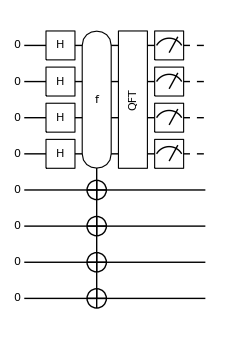

Let us look into the algorithm more closely. We prepare the control register in state

0↦H^(⊗m)0=1/(√(2^(m/2)))∑_(x=0)^(2^m-1) x

by applying the Hadamard gate on every qubit in the control register. The quantum oracle then makes the following transformation

1/(√(2^(m/2)))∑_(x=0)^(2^m-1) x⊗0->1/(√(2^(m/2)))∑_(x=0)^(2^m-1) x⊗f(x) .

We now replace states f(x) with F_k using the inverse relation,

f(x):=1/(√λ)∑_(k=0)^(λ-1) F_k ⅇ^(-2π ⅈ k x/λ),

which leads to the following expression for the final state of the total system

1/(√λ)∑_(k=0)^(λ-1) (1/(√(2^(m/2)))∑_(x=0)^(2^m-1) x ⅇ^(-2π ⅈ k x/λ))⊗F_k,

The above final state reveals that the quantum oracle has induced relative phase shifts in the control register that are proportional to the logical value x. As in the quantum phase estimation procedure, one can extract the relative phase shifts by employing the quantum Fourier transform. This corresponds to estimating the (normalized) “phase” k/λ, from which one can find the period λ (see below). In this sense, one can regard the period-finding problem to fall in the quantum phase estimation category.

Of course, one apparent difference is that the relative phase shifts are induced by the quantum oracle in this case. Furthermore, unlike the standard quantum phase estimation procedure, the phase k/λ to be estimated is randomly selected from the values corresponding to k=0,1,… ,λ−1. Specifically, the probability P_k for k to take a particular value is given by

P_k=F_kF_k/λ .

It is thus possible that the observed k may have a common divider with λ so that k/λ=k'/λ' for another pair of integers k' and λ'. For this reason, one cannot uniquely determine period λ from the recorded value of k/λ alone. The denominator (and the integer multiples of it) is only a candidate for the true period λ. However, it does not pose a serious obstacle given than it is easy to check if a candidate is the true period or not by evaluating the function for a few input values.

### Interim Demonstration

We demonstrate the basic ideas in the period-finding algorithm. More complete example follows below.

```mathematica
$n=4;
$N=Power[2,$n];
```

We take an example of the modular exponential function, f(x)=a^x (mod L) for a fixed a and L. Here a and L are assumed to be co-primes.

```mathematica
$a=3;
```

```mathematica
Clear[f];
f[k_Integer]:=PowerMod[$a,k,$N]
```

The function is periodic.

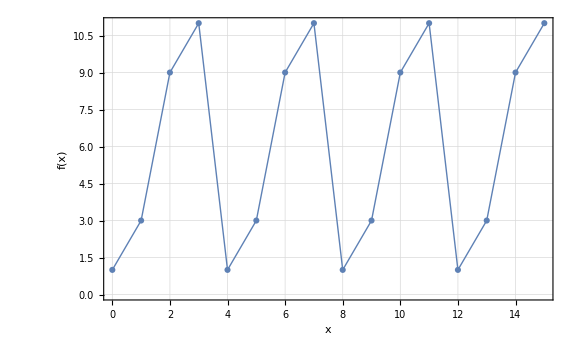

```mathematica
ListPlot[Table[{k,f[k]},{k,0,$N-1}],Joined->True,PlotMarkers->Automatic,FrameLabel->{"x",HoldForm@f[x]}]
```

Here is the quantum circuit model of the algorithm.

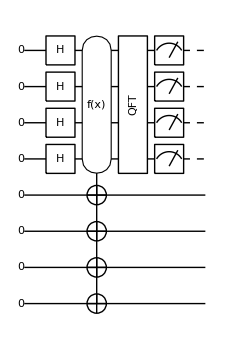

```mathematica
cc=Range[$n];
tt=Range[$n+1,$n+$n];
body=QuantumCircuit[Ket[Join[S@cc,S@tt]],
S[cc,6],Oracle[f,S@cc,S@tt],
QFT[S@cc]
];
qc=QuantumCircuit[body,Measurement@S[cc,3]]
```

```mathematica
EchoTiming[out=ExpressionFor[qc];]
ProductForm[out,{S@cc,S@tt}]
result=Readout@S[cc,3]
```

3.10721

1/2 1100⊗0001-1/2 ⅈ 1100⊗0011-1/2 1100⊗1001+1/2 ⅈ 1100⊗1011

{1,1,0,0}

From the measurement outcome, one can find the period. In this case, the period is 4.

```mathematica
frac=FromDigits[result,2]/$N
```

3/4

For a more complete overview, let us examine all possible outcomes.

```mathematica
new=ExpressionFor[body]
```

1/4 0_S_10_S_20_S_30_S_40_S_50_S_60_S_71_S_8+1/4 0_S_10_S_20_S_30_S_40_S_50_S_61_S_71_S_8+1/4 0_S_10_S_20_S_30_S_41_S_50_S_60_S_71_S_8+1/4 0_S_10_S_20_S_30_S_41_S_50_S_61_S_71_S_8+1/4 0_S_11_S_20_S_30_S_40_S_50_S_60_S_71_S_8+1/4 ⅈ 0_S_11_S_20_S_30_S_40_S_50_S_61_S_71_S_8-1/4 0_S_11_S_20_S_30_S_41_S_50_S_60_S_71_S_8-1/4 ⅈ 0_S_11_S_20_S_30_S_41_S_50_S_61_S_71_S_8+1/4 1_S_10_S_20_S_30_S_40_S_50_S_60_S_71_S_8-1/4 1_S_10_S_20_S_30_S_40_S_50_S_61_S_71_S_8+1/4 1_S_10_S_20_S_30_S_41_S_50_S_60_S_71_S_8-1/4 1_S_10_S_20_S_30_S_41_S_50_S_61_S_71_S_8+1/4 1_S_11_S_20_S_30_S_40_S_50_S_60_S_71_S_8-1/4 ⅈ 1_S_11_S_20_S_30_S_40_S_50_S_61_S_71_S_8-1/4 1_S_11_S_20_S_30_S_41_S_50_S_60_S_71_S_8+1/4 ⅈ 1_S_11_S_20_S_30_S_41_S_50_S_61_S_71_S_8

```mathematica
data=Table[Measurement[S[cc,3]]@new;FromDigits[Readout[S[cc,3]],2],{15}]
```

{0,4,4,12,12,8,12,0,0,12,0,12,4,12,8}

```mathematica
sec=Union[data/$N]
```

{0,1/4,1/2,3/4}

The period must be 4, which agrees with the true value.

Post-Processing: Continued Fraction Method

A more serious hurdle is that the estimated phase ϕ is only approximate, ϕ ≈ k/λ, to the precise value k/λ because the register is of finite size. This deviation makes it even harder to determine the period λ from the estimated phase ϕ. Fortunately, a continued fraction representation provides an efficient method to find the period in such a situation.

### Continued Fraction

A continued fraction is an expression of the form

a_0+1/(a_1+1/(a_2+1/(⋱+1/a_n))) ,

where a_0,a_1,a_2,…,a_n are positive integers (there are several other conventions for continued fractions, and here we only use the so-called simple or canonical continued fractions). It is often denoted by

[a_0;a_1,a_2,…,a_n] .

One can represent any real number with a unique continued fraction. (For a finite continued fraction, there is a trivial ambiguity such as [a_0;a_1,a_2,…,a_n]=[a_0;a_1,a_2,…,a_n-1,1]. We regard such continued fractions to be equivalent.) For a given number, the procedure to find a continued fraction is simple. For example, consider 13/5. We first split it into its integer part which is 2 and fractional part 3/5, so 13/5=2+3/5. Next, we take the reciprocal of 3/5 and split it into its integer and fractional parts, 5/3=1+2/3. By repeating the procedure, we find that

13/5=2+1/(1+1/(1+1/2))=[2;1,1,2].

The well-known Euclidean algorithm, dating back to Euclid’s book Elements, provides an efficient method to find a continued fraction representation of a number. A continued fraction may be terminated after a finite number of steps, and in such case is said to be finite. If a continued fraction continues the iteration without termination, then it is called an infinite continued fraction.

Although not so common in daily life, continued fraction representations are, in many respects, more natural mathematically than the decimal representations or other similar representations with a fixed base. To see this, consider the following properties: The continued fraction for any rational number is finite, which stands in contrast with decimal representations. For example, 5/3 = [1; 1, 2] whereas 5/3 = 1.666 · · · . On the other hand, continued fractions for irrational numbers are infinite. For example, the golden ratio is represented by the continued fraction, (1+√5)/2=[1;1,1,1,⋯ ]. Furthermore, continued fractions for a number and its reciprocal are identical except for a shift by one place. In other words, [a_0;a_1,a_2,…,a_n] and [0;a_0,a_1,a_2,…,a_n] are reciprocal of each other.

Continued fraction convergents are often used to approximate irrational numbers by rational ones. More specifically, given a (possibly irrational) number x and its continued fraction representation x=[a_0;a_1,a_2,…,a_m,a_(m+1),…,a_n]  (with n possibly being infinity), the m^th convergent of the continued fraction is defined by p/q:=[a_0;a_1,a_2,…,a_m] (0≤m≤n) and p/q approximates x (p/q≈x). Those approximations alternate from above and below, and converge exponentially in the number m of terms. Furthermore, a convergent p/q of a simple continued fraction is better than any other rational approximation with denominator less than or equal to q.

### Determination of the Period

The method to determine the period λ from the estimated phase, ϕ≈k/λ, is based on a theorem from number theory. It states that if

|k/λ-ϕ|≤1/(2 λ^2)

for any integers k and λ, then k/λ is a convergent of the continued fraction for ϕ. Note that ϕ is accurate to m bits. The error is less than 2^-m with probability higher than 0.81 (see Quantum Phase Estimation). Since λ≪2^m, the above condition is satisfied. Therefore, the continued fraction of the estimated phase ϕ gives coprimes k'/λ' such that k'/λ'=k/λ. λ' and integer multiples of λ' are candidates for the period. We then evaluate (classically) the function to check if λ (or any integer multiple of λ') is the true period λ of the function.

Demonstration

Now we consider a full period-finding problem. We consider a four-qubit system.

```mathematica
$n=4;
$N=Power[2,$n];
```

We define an arbitrary function with period 3.

```mathematica
f[0]=1;f[1]=5;f[2]=4;
f[x_Integer]:=f[Mod[x,3]]
```

This plot illustrates that the function is indeed periodic with period 3.

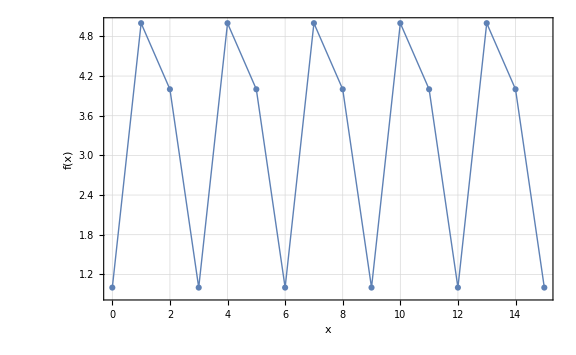

```mathematica
ListPlot[Table[{k,f[k]},{k,0,$N-1}],Joined->True,PlotMarkers->Automatic,FrameLabel->{"x",HoldForm@f[x]}]
```

Here is the quantum circuit model of the algorithm.

```mathematica
cc=Range[$n];
tt=Range[$n+1,$n+$n];
body=QuantumCircuit[Ket[Join[S@cc,S@tt]],
S[cc,6],Oracle[f,S@cc,S@tt],
QFT[S@cc,N->True]
];
qc=QuantumCircuit[body,Measurement@S[cc,3]]
```

-Graphics-

This is a full run of the above quantum circuit model.

```mathematica
EchoTiming[out=ExpressionFor[qc];]
result=Readout@S[cc,3]
```

4.57572

{1,0,1,1}

In order to check more random results, it is more efficient to first calculate the output state right before the measurement.

```mathematica
EchoTiming[new=ExpressionFor[body];]
```

3.53635

From the above output state, we perform measurements (as many times as we like) to get random results.

```mathematica
out=Measurement[S[cc,3]]@N[new];
phi=FromDigits[Readout@S[cc,3],2]/$N
```

3/16

From the above random result, we determine the period of the function by utilizing the continued fraction representation of the estimated phase.

```mathematica
cnt=ContinuedFraction[phi]
candidates=Convergents[cnt]
```

{0,5,3}

{0,1/5,3/16}

From the above convergents, we have two candidates 3 (and its multiples 6, 9, 12, 15 are also candidates) and 16. Evaluation of the function for some arguments confirms that 3 is the period of the function.

| Related Guides
▪Quantum Information Systems

| Related Tech Notes
▪Abelian Hidden Subgroup Problems
▪Quantum Algorithms
▪Quantum Information Systems with Q3

| Related Links
▪M. Nielsen and I. L. Chuang (2022)https://doi.org/10.1017/CBO9780511976667, Quantum Computation and Quantum Information (Cambridge University Press, 2011).
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer, 2022).